```mathematica
Msol := 1989*10^(30) (*en gramos*)
m0 :=10^9*Msol
ab := Rationalize[7.41*10^(-9), 0] (*adimensional*)
mb := m0*ab
ηb := Rationalize[2.19*10^4,0]  (*en segundos*)
ηi := Rationalize[2.96*10^(12),0]   (*en segundos*)
G := 6.674*10^(-8)  (*en cgs*)
c := 2.998*10^(10)   (*en cgs*)
σ :=Rationalize[(81*G)/(8*c^3)*1/(ab*ηb), 0]
xi :=Rationalize[ηi/ηb, 0]
```

```mathematica
Mandin[x_]:= mb*(1+x^2)^(1/2)
```

```mathematica
g[x_]:=(σ*x^3)/(3*(x^2+1)^(3/2))
Manac[x_] := 1/(1/m0-(g[x]-g[xi]))
```

```mathematica
Plot[{Mandin[x],Manac[x]},{x,-xi,xi},PlotLegends->{"dinámica","acreción"}]
```

-Graphics-

```mathematica
N[Mandin[xi]]
```

1.99205×10^37

```mathematica
N[Manac[xi]]
```

1.989×10^37

```mathematica
prueba[x_]:=Mandin[x]/Manac[x]
```

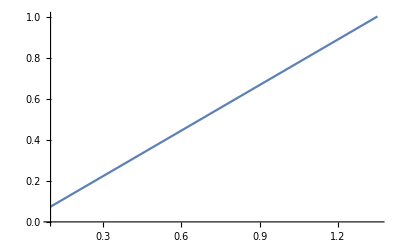

```mathematica
Plot[prueba[x], {x, 10^7, xi}]
```

```mathematica
N[prueba[0]]
```

0.759199

```mathematica
N[prueba[-10]]
```

15.1467

```mathematica
N[prueba[-xi]]
```

2.05226×10^8

```mathematica
D[prueba[x], x]
```

147384900000000000000000000000 √(1+x^2) (x^4/(6471068157982913314651971796639598 (1+x^2)^(5/2))-x^2/(6471068157982913314651971796639598 (1+x^2)^(3/2)))+1/(√(1+x^2))147384900000000000000000000000 x (1/19890000000000000000000000000000000000+12967168000000000000000000000000/(8504536615947464460186557301543383501554829007947639517 √876160000000000047961)-x^3/(19413204473948739943955915389918794 (1+x^2)^(3/2)))